```mathematica
(*cálculo da distancia ao centro da terra a partir da altitude*)
```

```mathematica
a=6.378137;
```

```mathematica
b=6.356752314245;
```

```mathematica
s[la_]:=a^2/Sqrt[a^2*Cos[la]^2+b^2*Sin[la]^2]
```

```mathematica
(*leitura de momentos multipolares do excel*)
```

```mathematica
mg=Import["C:\\Users\\Utilizador\\Documents\\astropi\\wmg2.csv"];
```

```mathematica
mh=Import["C:\\Users\\Utilizador\\Documents\\astropi\\wmh2.csv"];
```

```mathematica
(*construcao das matrizes dos momentos multipolares*)
```

```mathematica
h=Table[0,{i,3},{j,1,14}];
```

```mathematica
g=Table[0,{i,3},{j,1,14}];
```

```mathematica
Do[g[[i,j]]=mg[[i*(i+1)/2-1+j]][[1]],{i,1,3},{j,1,i+1}]
```

```mathematica
Do[h[[i,j]]=mh[[i*(i+1)/2-1+j]][[1]],{i,1,3},{j,1,i+1}]
```

```mathematica
(*raio da terra no modelo multipolar e ordem da expansao*)
```

```mathematica
rt=6.3712;
```

```mathematica
n=3;
```

```mathematica
(*campo no modelo multipolar*)
```

```mathematica
V[r_,la_,lo_]:=rt*Sum[(rt/r)^(i+1)*(g[[i,j]]*Cos[(j-1)*lo]+h[[i,j]]*Sin[(j-1)*lo])*LegendreP[i,j-1,Sin[la]]*(-1)^(j-1)*Sqrt[(2-KroneckerDelta[j,1])*(i-j+1)!/(i+j-1)!],{i,1,n},{j,1,i+1}]/1000
```

```mathematica
dvr[r_,la_,lo_]:=D[V[x,la,lo],x]/.x->r
```

```mathematica
dvla[r_,la_,lo_]:=D[V[r,x,lo],x]/r/.x->la
```

```mathematica
dvlo[r_,la_,lo_]:=D[V[r,la,x],x]/r/Cos[la]/.x->lo
```

```mathematica
Bx[la_,lo_]:=(-Cos[la]*dvr[s[la],la,lo]+Sin[la]*dvla[s[la],la,lo])*Cos[lo]+Sin[lo]*dvlo[s[la],la,lo]
```

```mathematica
By[la_,lo_]:=(-Cos[la]*dvr[s[la],la,lo]+Sin[la]*dvla[s[la],la,lo])*Sin[lo]-Cos[lo]*dvlo[s[la],la,lo]
```

```mathematica
Bz[la_,lo_]:=-Sin[la]*dvr[s[la],la,lo]-Cos[la]*dvla[s[la],la,lo]
```

```mathematica
(*modulo do campo no modelo multipolar*)
```

```mathematica
B[la_,lo_]:=Sqrt[Bx[la,lo]^2+By[la,lo]^2+Bz[la,lo]^2]
```

```mathematica
Bminsul[la_,lo_]:=Sqrt[Bx[la,lo]^2+By[la,lo]^2+Bz[la,lo]^2]-(Bx[la,lo]*Cos[la]*Cos[lo]+By[la,lo]*Cos[la]*Sin[lo]+Bz[la,lo]*Sin[la])
```

```mathematica
Bminnor[la_,lo_]:=Sqrt[Bx[la,lo]^2+By[la,lo]^2+Bz[la,lo]^2]+(Bx[la,lo]*Cos[la]*Cos[lo]+By[la,lo]*Cos[la]*Sin[lo]+Bz[la,lo]*Sin[la])
```

```mathematica
NMinimize[Bminsul[la1,lo1],{la1,lo1}]
```

{-7.10543×10^-15,{la1→-2.13374,lo1→-3.42086}}

```mathematica
Bminsul[-Pi+2.133740874908845,2*Pi-3.420861796469678]
```

7.10543×10^-15

```mathematica
Bminsul[-2.113573847019043,-3.8712067495978664]
```

-7.10543×10^-15

```mathematica
-Pi+2.133740874908845
```

-1.00785

```mathematica
2*Pi-3.420861796469678
```

2.86232

```mathematica
NMinimize[Bminnor[lati,long],{lati, long}]
```

{-7.10543×10^-15,{lati→1.23238,long→1.39573}}

```mathematica
1.2323763521197897*180/Pi
```

70.61

```mathematica
1.3957319781177757*180/Pi
```

79.9696

```mathematica
gra1=ListPlot[{{1.3957319781177757,1.2323763521197897},{2.862323510709908,-1.0078517786809482}},PlotRange->{{-Pi,Pi},{-Pi/2,Pi/2}},AspectRatio->1/2,Ticks->None,Frame->None,PlotStyle->{Red,PointSize[0.02]},Axes->None]
```

-Graphics-

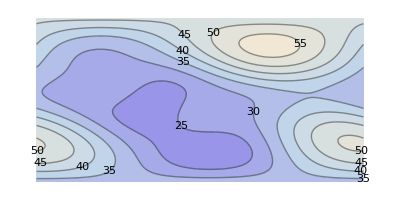

```mathematica
gra2=ContourPlot[B[la,lo],{lo,-Pi,Pi},{la,-Pi/2,Pi/2},AspectRatio->1/2,Ticks->None,Frame->None,ContourLabels->True]
```

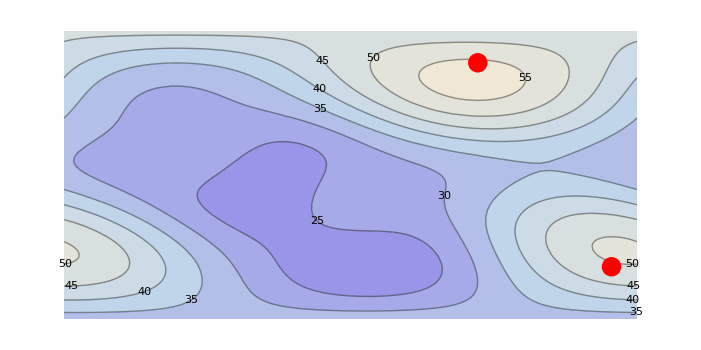

```mathematica
Show[gra2,gra1]
```